```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 229 Kb

{Utilities`CleanSlate`,TriangleLink`,CompiledFunctionTools`,IPOPTLink`,VariationalMethods`,DocumentationSearch`,ResourceLocator`,System`,Global`,Graphics`Mesh`,Graphics`PolygonUtils`}

```mathematica
Clear[zReplace]
zReplace = 
z[t] -> A r[t]^2
```

z[t]→A r[t]^2

```mathematica
D[zReplace, t]
```

z'[t]→2 A r[t] r'[t]

```mathematica
Clear[s]
s = { r[t] Cos[ϕ[t]]  ,r[t] Sin[ϕ[t]] , z[t] }
```

{Cos[ϕ[t]] r[t],r[t] Sin[ϕ[t]],z[t]}

```mathematica
D[s, t]
```

{Cos[ϕ[t]] r'[t]-r[t] Sin[ϕ[t]] ϕ'[t],Sin[ϕ[t]] r'[t]+Cos[ϕ[t]] r[t] ϕ'[t],z'[t]}

```mathematica
D[s, t] . D[s, t]
```

z'[t]^2+(Sin[ϕ[t]] r'[t]+Cos[ϕ[t]] r[t] ϕ'[t])^2+(Cos[ϕ[t]] r'[t]-r[t] Sin[ϕ[t]] ϕ'[t])^2

```mathematica
D[s, t] . D[s, t]  // Expand
```

Cos[ϕ[t]]^2 r'[t]^2+Sin[ϕ[t]]^2 r'[t]^2+z'[t]^2+Cos[ϕ[t]]^2 r[t]^2 ϕ'[t]^2+r[t]^2 Sin[ϕ[t]]^2 ϕ'[t]^2

```mathematica
D[s, t] . D[s, t]  // Expand  // Simplify
```

r'[t]^2+z'[t]^2+r[t]^2 ϕ'[t]^2

```mathematica
s
s[[3]]
m g ( s[[3]] ) 
m g ( s[[3]] )  /. zReplace
```

{Cos[ϕ[t]] r[t],r[t] Sin[ϕ[t]],z[t]}

z[t]

g m z[t]

A g m r[t]^2

```mathematica
Clear[V]
V = m g ( s[[3]] )  /. zReplace
```

A g m r[t]^2

```mathematica
1/2 m ( D[s, t] . D[s, t]  // Expand  // Simplify  ) 
(1/2 m ( D[s, t] . D[s, t]  // Expand  // Simplify  ) ) /. zReplace /. D[zReplace, t]  // Expand
```

1/2 m (r'[t]^2+z'[t]^2+r[t]^2 ϕ'[t]^2)

1/2 m r'[t]^2+2 A^2 m r[t]^2 r'[t]^2+1/2 m r[t]^2 ϕ'[t]^2

```mathematica
Clear[T]
T = 
(1/2 m ( D[s, t] . D[s, t]  // Expand  // Simplify  ) ) /. zReplace /. D[zReplace, t]  // Expand 
T // pdConv
```

1/2 m r'[t]^2+2 A^2 m r[t]^2 r'[t]^2+1/2 m r[t]^2 ϕ'[t]^2

2 A^2 m (r(t))^2 ((∂r(t))/(∂t))^2+1/2 m (r(t))^2 ((∂ϕ(t))/(∂t))^2+1/2 m ((∂r(t))/(∂t))^2

```mathematica
Clear[ℒ]
ℒ = T - V  ;
ℒ // pdConv
```

2 A^2 m (r(t))^2 ((∂r(t))/(∂t))^2-A g m (r(t))^2+1/2 m (r(t))^2 ((∂ϕ(t))/(∂t))^2+1/2 m ((∂r(t))/(∂t))^2

```mathematica
Clear[q]
q  = { r[t] , ϕ[t] }
```

{r[t],ϕ[t]}

```mathematica
Clear[ eqs ] 
eqs = 
EulerEquations[ ℒ , q , t ] ;
eqs // TableForm
```

-m (r[t] (2 A g+4 A^2 r'[t]^2-ϕ'[t]^2)+r''[t]+4 A^2 r[t]^2 r''[t])==0
-m r[t] (2 r'[t] ϕ'[t]+r[t] ϕ''[t])==0

```mathematica
Clear[parameters]
parameters = {
m-> 1 , 
A-> 1 ,
g-> 9.8
};
parameters // TableForm
```

m→1
A→1
g→9.8

```mathematica
eqs /. parameters // Expand  // TableForm
```

-19.6 r[t]-4 r[t] r'[t]^2+r[t] ϕ'[t]^2-r''[t]-4 r[t]^2 r''[t]==0
-2 r[t] r'[t] ϕ'[t]-r[t]^2 ϕ''[t]==0

```mathematica
Clear[ics]
ics = {
r[0] == 0.1 ,
r'[0] == 0.2 ,
ϕ[0] == 0.1 ,
ϕ'[0] == 0.2
} ;
ics // TableForm
```

r[0]==0.1
r'[0]==0.2
ϕ[0]==0.1
ϕ'[0]==0.2

```mathematica
Clear[solution]
solution[t_] = 
First[NDSolve[  Union[ eqs /. parameters , ics ] , q , { t, 0, 100 } ] ]
```

{r[t]→InterpolatingFunction[{{0., 100.}}, <>][t],ϕ[t]→InterpolatingFunction[{{0., 100.}}, <>][t]}

```mathematica
Plot[ Evaluate[ q /. solution[t]]  , { t, 0, 10 }, PlotLabels-> q  ]
```

-Graphics-

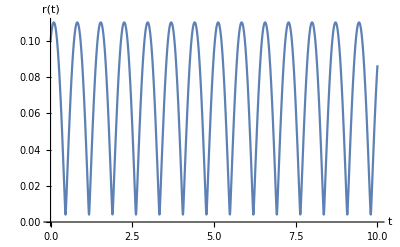

```mathematica
Plot[ Evaluate[ q[[1]] /. solution[t]]  , { t, 0, 10 }, AxesLabel->{ t,  q[[1]] }  ]
```

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[1,2]] , solution'[t][[1,2]] } , { t , 0, tmax } , AxesLabel-> { q[[1]] , D[q[[1]], t] } ]  ,
{ tmax , 1 ,75 , 0.5  } ]
```

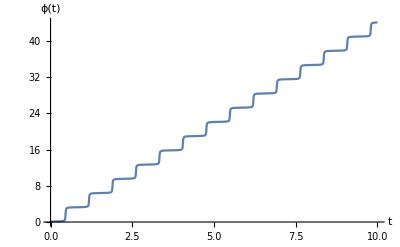

```mathematica
Plot[ Evaluate[ q[[2]] /. solution[t]]  , { t, 0, 10 }, AxesLabel->{ t,  q[[2]] }  ]
```

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[2,2]] , solution'[t][[2,2]] } , { t , 0, tmax } , AxesLabel-> { q[[2]] , D[q[[2]], t] } ]  ,
{ tmax , 1 ,0.25 , 0.001  } ]
```

```mathematica
D[q, t]
D[q[[1]], t]
D[q[[2]], t]
```

{r'[t],ϕ'[t]}

r'[t]

ϕ'[t]

```mathematica
D[ ℒ , D[q[[1]], t] ]
```

m r'[t]+4 A^2 m r[t]^2 r'[t]

```mathematica
q
```

{r[t],ϕ[t]}

```mathematica
Clear[𝓅]
𝓅 = Map[ p , q ]
```

{p[r[t]],p[ϕ[t]]}

```mathematica
𝓅[[1]]
𝓅[[2]]
```

p[r[t]]

p[ϕ[t]]

```mathematica
Table[  D[ ℒ , D[q[[i]], t] ]== 𝓅[[i]]   , { i, 1, 2 } ]  // TableForm
```

m r'[t]+4 A^2 m r[t]^2 r'[t]==p[r[t]]
m r[t]^2 ϕ'[t]==p[ϕ[t]]

```mathematica
Clear[momenta]
momenta = 
Flatten[Solve[ Table[  D[ ℒ , D[q[[i]], t] ]== 𝓅[[i]]   , { i, 1, 2 } ] , D[q, t] ] ]
```

{r'[t]→p[r[t]]/(m (1+4 A^2 r[t]^2)),ϕ'[t]→p[ϕ[t]]/(m r[t]^2)}

```mathematica
𝓅
```

{p[r[t]],p[ϕ[t]]}

```mathematica
D[q, t]
```

{r'[t],ϕ'[t]}

```mathematica
Collect[ ℒ  , r'[t] ]  // pdConv
```

((∂r(t))/(∂t))^2 (2 A^2 m (r(t))^2+m/2)-A g m (r(t))^2+1/2 m (r(t))^2 ((∂ϕ(t))/(∂t))^2

```mathematica
Sum[ 𝓅[[i]] D[q[[i]], t] , { i, 1, 2 } ] - ℒ  // Simplify
```

p[r[t]] r'[t]-1/2 m r'[t]^2+p[ϕ[t]] ϕ'[t]-1/2 m r[t]^2 (-2 A g+4 A^2 r'[t]^2+ϕ'[t]^2)

```mathematica
Sum[ 𝓅[[i]] D[q[[i]], t] , { i, 1, 2 } ] - ℒ  /. momenta  //FullSimplify // Apart 
(* God damn this is right!!! *)
```

p[ϕ[t]]^2/(2 m r[t]^2)+A g m r[t]^2+p[r[t]]^2/(2 m (1+4 A^2 r[t]^2))

```mathematica
Clear[ℋ]
ℋ = Sum[ 𝓅[[i]] D[q[[i]], t] , { i, 1, 2 } ] - ℒ  /. momenta  //FullSimplify // Apart
```

p[ϕ[t]]^2/(2 m r[t]^2)+A g m r[t]^2+p[r[t]]^2/(2 m (1+4 A^2 r[t]^2))

```mathematica
ℋ  // pdConv
```

(p(r(t)))^2/(2 m (4 A^2 (r(t))^2+1))+A g m (r(t))^2+(p(ϕ(t)))^2/(2 m (r(t))^2)